```mathematica
pPrime=1/(√5){2,1}; (* u *)
pPP = 9/40{-1,-11}; (* v *)
(pPrime.pPP)/(pPrime.pPrime)pPrime
```

{-117/100,-117/200}

```mathematica
pPP-{-117/100,-117/200}
```

{189/200,-189/100}

```mathematica
Norm[{189/200,-189/100}]//N
```

2.11308

```mathematica
r[t_]:={
-10 t^3+9 t^2+1,
10 t^3-21 t^2+12t
}
r[1/3]
```

{44/27,55/27}

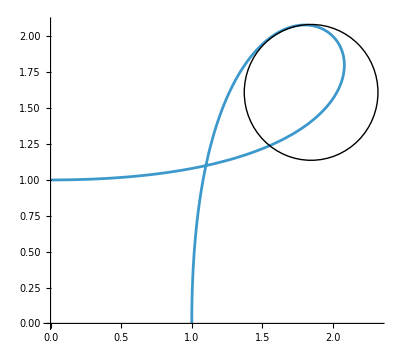

```mathematica
Show[
ParametricPlot[r[t],{t,0,1}],
Graphics[Circle[r[1/3]+1/2.113{{0,1},{-1,0}}.((1/(√5){2,1})/Norm[1/(√5){2,1}]),1/2.113]],
PlotRange->All
]
```